## EdgeVertices-example.nb

Example Cellzilla2D notebook.

LGPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Thu 8 Jun 2017 11:30:32
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

```mathematica
w=TemplateRandomCircularGrid[15,100];
```

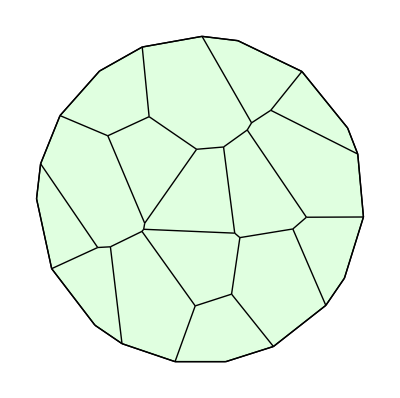

```mathematica
ShowTissue[w]
```

```mathematica
ev=EdgeVertices[w]
```

{{{-55.445,23.8469},{-50.085,35.9318}},{{-55.445,23.8469},{-40.8944,-32.3056}},{{-55.445,23.8469},{-99.9899,1.42045}},{{-53.311,41.4137},{-50.085,35.9318}},{{-53.311,41.4137},{-30.3926,95.2696}},{{-53.311,41.4137},{-78.9758,61.3419}},{{-50.085,35.9318},{-18.1793,26.9718}},{{-40.8944,-32.3056},{-37.8643,-34.1456}},{{-40.8944,-32.3056},{-94.2883,-33.3123}},{{-37.8643,-34.1456},{-23.2444,-28.7446}},{{-37.8643,-34.1456},{-55.2138,-83.3753}},{{-23.2444,-28.7446},{-19.0731,-23.3876}},{{-23.2444,-28.7446},{15.9875,-65.5657}},{{-19.0731,-23.3876},{-18.1793,26.9718}},{{-19.0731,-23.3876},{30.6009,-11.0834}},{{-18.1793,26.9718},{-4.58989,31.7337}},{{-4.58989,31.7337},{13.8076,60.4942}},{{-4.58989,31.7337},{34.2054,-5.32325}},{{13.8076,60.4942},{32.1543,53.7081}},{{13.8076,60.4942},{12.7871,99.1791}},{{15.9875,-65.5657},{32.4002,-69.9956}},{{15.9875,-65.5657},{-27.4589,-96.1562}},{{30.6009,-11.0834},{32.433,-69.8795}},{{30.6009,-11.0834},{34.2054,-5.32325}},{{32.1543,53.7081},{49.8868,1.37232}},{{32.1543,53.7081},{70.0703,71.3453}},{{32.4002,-69.9956},{32.433,-69.8795}},{{32.4002,-69.9956},{42.0073,-90.7491}},{{32.433,-69.8795},{91.9298,-39.3562}},{{34.2054,-5.32325},{49.8868,1.37232}},{{49.8868,1.37232},{51.9915,1.4528}},{{51.9915,1.4528},{90.8321,41.8273}},{{51.9915,1.4528},{98.2398,-18.6802}},{{98.3849,17.8999},{90.8321,41.8273}},{{98.3849,17.8999},{98.2398,-18.6802}},{{50.8408,86.1116},{70.0703,71.3453}},{{50.8408,86.1116},{12.7871,99.1791}},{{-48.0299,87.7105},{-30.3926,95.2696}},{{-48.0299,87.7105},{-78.9758,61.3419}},{{-96.8703,24.8223},{-78.9758,61.3419}},{{-96.8703,24.8223},{-99.9899,1.42045}},{{-80.3764,-59.4948},{-94.2883,-33.3123}},{{-80.3764,-59.4948},{-55.2138,-83.3753}},{{-6.33276,-99.7993},{-27.4589,-96.1562}},{{-6.33276,-99.7993},{42.0073,-90.7491}},{{80.2064,-59.7238},{42.0073,-90.7491}},{{80.2064,-59.7238},{91.9298,-39.3562}},{{90.8321,41.8273},{70.0703,71.3453}},{{12.7871,99.1791},{-30.3926,95.2696}},{{-99.9899,1.42045},{-94.2883,-33.3123}},{{-55.2138,-83.3753},{-27.4589,-96.1562}},{{91.9298,-39.3562},{98.2398,-18.6802}}}

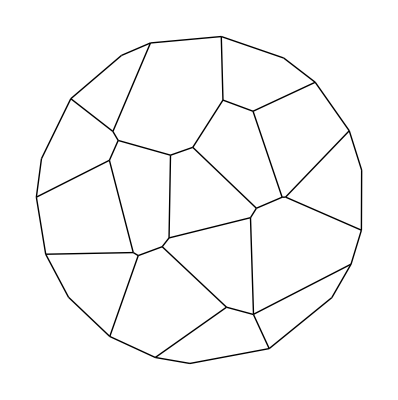

```mathematica
Graphics[Line/@ev]
```